### Settings

```mathematica
dx = 4.58/0.529;
dy = 6.48/0.529;
a=132.7/0.529;
delta =0.01;
rMax=200; 
Z = 0.095; 
m = 0.02;
coord = {{-5*dx,0},{5*dx,0},{0,-4*dy},{0,4*dy},{4*dx, 3*dy},{4*dx, -3*dy},{-4*dx, 3*dy},{-4*dx, -3*dy}};
```

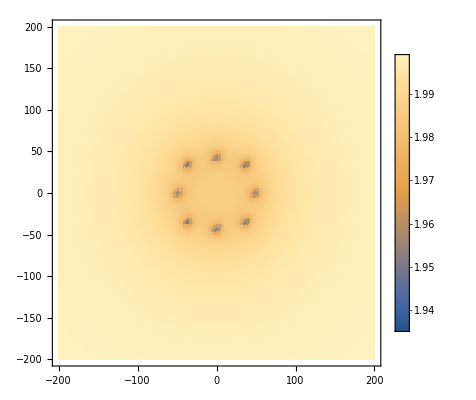

```mathematica
V[r_, θ_] := Sum[(-Z)/(Sqrt[(r*Sin[θ]- coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]+delta)*Exp[-Sqrt[(r*Sin[θ]-coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]/a],{i,8} ] +2;
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->200];*)
(*Plot[V[r ,θ]/.r->x/.θ-> 0, {x, 0,rMax},PlotRange->All]
Export[NotebookDirectory[]<>"Coulomb_line.png",%,ImageResolution->100];*)
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/(2*m))* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{1.99219,2.00001,2.00019,2.00378,2.00544,2.00546,2.00945,2.00963}

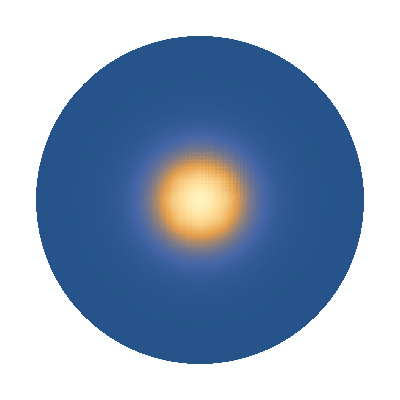

```mathematica
F1 =Part[Re[egnVec],Part[ord,1]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-1.5*rMax,1.5*rMax},{y,-1.5*rMax,1.5*rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-1.5*rMax,1.5*rMax},{y,-1.5*rMax,1.5*rMax}, PlotTheme->"Minimal", PlotPoints->200,PlotRange->All  (*PlotLegends->Automatic*)];
Show[{%,%%}]
(*Export[NotebookDirectory[]<>"3.png",%,ImageResolution->600];*)
```

```mathematica
str=OpenWrite[NotebookDirectory[]<>"data.dat", FormatType->StandardForm];
$Output={str};
Do[Print[x ,"  ",  F1/.r->x/.θ->0.5235987], {x, 0, rMax, 0.1 }];
Close[str];
```